```mathematica
ClearAll["Global`*"]
Needs["Notation`"]
Symbolize[Subscript[m, _]];
Symbolize[Subscript[P, _]];
Symbolize[Subscript[_, s]];
Symbolize[_^*]; 
Symbolize[Subscript[a, _]];
(*TEST
Subscript[P, 2]=5
θ^*=2
Subscript[P, 2]+θ^*
*)
```

```mathematica
Clear[Subscript[m, W],Subscript[m, t],P,q,λ];
Subscript[P, top]={Subscript[P, x],Subscript[P, y],Subscript[P, z]}; (*more generic polarization, still in the x'y'z' top rest frame*)
Subscript[P, anti]={Subscript[P, x],Subscript[P, y],Subscript[P, z]}; (*more generic polarization, still in the x'y'z' top rest frame*)
Subscript[P, top]={{{0,0,0.9}}, {{0,0,1}}}; (*top polarization +1, along the direction of the spectator quark in the x'y'z' top rest frame*)
(* https://indico.cern.ch/event/672995/contributions/2753818/attachments/1542125/2418890/Carlos_-_EFT_interpretation_-_17.10.2017.pdf*)
Subscript[P, top]={0.,0,0.88};
Subscript[P, anti]={-0.11,0,-0.85};
R=RotationMatrix[-Subscript[θ, s],{0,1,0}].RotationMatrix[-Subscript[ϕ, s],{0,0,1}]; (* rotation from xyz to x'y'z' *)
Rinv=Inverse[R];  (* rotation from x'y'z' to xyz *)

uL={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
uT={Cos[θ]*Cos[ϕ],Cos[θ]*Sin[ϕ],-Sin[θ]};
uN={Sin[ϕ],-Cos[ϕ],0};

(* DIFFERENTIAL SOLID ANGLE TERM, dΩ=Sin[θ]dθdϕ *)
J=Sin[θ]; 
SuperStar[J]=Sin[SuperStar[θ]]; 

Subscript[a, 0]=(Subscript[m, t]^2-Subscript[m, W]^2-2 Subscript[m, t] q)/Subscript[m, t]^2;
Subscript[a, 1]=Subscript[m, t]^2/(2 Subscript[m, W]^2)(Subscript[m, t]^2-Subscript[m, W]^2+2 Subscript[m, t] q)/Subscript[m, t]^2;
Subscript[a, 2]=Subscript[m, t]^2/(2 Subscript[m, W]^2)(Subscript[m, t]^2-Subscript[m, W]^2-2 Subscript[m, t] q)/Subscript[m, t]^2;
Subscript[a, 3]=(Subscript[m, t]^2-Subscript[m, W]^2+2 Subscript[m, t] q)/Subscript[m, t]^2;
Subscript[a, 4][SuperStar[ϕ]:_]:=Subscript[m, t]/(√2 Subscript[m, W])(Subscript[m, t]^2-Subscript[m, W]^2-2 Subscript[m, t] q)/Subscript[m, t]^2 Cos[SuperStar[ϕ]]; 
Subscript[a, 5][SuperStar[ϕ]:_]:=Subscript[m, t]/(√2 Subscript[m, W])(Subscript[m, t]^2-Subscript[m, W]^2+2 Subscript[m, t] q)/Subscript[m, t]^2 Cos[SuperStar[ϕ]]; 
Subscript[a, 6][SuperStar[ϕ]:_]:=Subscript[m, t]/(√2 Subscript[m, W])(Subscript[m, t]^2-Subscript[m, W]^2-2 Subscript[m, t] q)/Subscript[m, t]^2(-Sin[SuperStar[ϕ]]); 
Subscript[a, 7][SuperStar[ϕ]:_]:=Subscript[m, t]/(√2 Subscript[m, W])(Subscript[m, t]^2-Subscript[m, W]^2+2 Subscript[m, t] q)/Subscript[m, t]^2(-Sin[SuperStar[ϕ]]);
NORM=Subscript[a, 0]+Subscript[a, 1]+Subscript[a, 2]+Subscript[a, 3];
```

```mathematica
(* CONSTRUCT THE FULLY DIFFERENTIAL CROSS SECTION, FUNCTION OF (θ,ϕ,θ^*,ϕ^*) *)

Clear[Subscript[m, W],Subscript[m, t],q];
TopPDF[θ_,ϕ_,SuperStar[θ]:_,SuperStar[ϕ]:_,λ_,P:_] :=3/(64 π^2 NORM)(( Subscript[a, 0](1+λ Cos[SuperStar[θ]])^2 + 2 Subscript[a, 1] Sin[SuperStar[θ]]^2)(1+P.uL)+
                                                           (2 Subscript[a, 2] Sin[SuperStar[θ]]^2 + Subscript[a, 3](1-λ Cos[SuperStar[θ]])^2)(1-P.uL) +
                                                              2 √2 λ(Subscript[a, 4][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 5][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uT+
                                                              2 √2 λ(Subscript[a, 6][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 7][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uN)J SuperStar[J]
ProbTop=TopPDF[θ,ϕ,SuperStar[θ],SuperStar[ϕ],1,Subscript[P, top]] 
Simplify[ProbTop]
```

(3 Sin[θ] Sin[θ^*] (0.+2 √2 (((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*]) Cos[ϕ^*])/(√2 m_t m_W)+((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*]) Cos[ϕ^*])/(√2 m_t m_W)) (0.-0.88 Sin[θ]) Sin[θ^*]+(1.-0.88 Cos[θ]) (((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*])^2)/m_t^2+((m_t^2-m_W^2-2 m_t q) Sin[θ^*]^2)/m_W^2)+(1.+0.88 Cos[θ]) (((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*])^2)/m_t^2+((m_t^2-m_W^2+2 m_t q) Sin[θ^*]^2)/m_W^2)))/(64 π^2 ((m_t^2-m_W^2-2 m_t q)/m_t^2+(m_t^2-m_W^2-2 m_t q)/(2 m_W^2)+(m_t^2-m_W^2+2 m_t q)/m_t^2+(m_t^2-m_W^2+2 m_t q)/(2 m_W^2)))

-1/(m_t^4+1. m_t^2 m_W^2-2. m_W^4)0.016718 Sin[θ] Sin[θ^*] (-0.568182 m_t^2 m_W^2+0.568182 m_W^4+(-0.568182 m_t^2 m_W^2+0.568182 m_W^4) Cos[θ^*]^2+1. m_t^3 m_W Cos[ϕ^*] Sin[θ] Sin[θ^*]-1. m_t m_W^3 Cos[ϕ^*] Sin[θ] Sin[θ^*]-0.568182 m_t^4 Sin[θ^*]^2+0.568182 m_t^2 m_W^2 Sin[θ^*]^2+m_t m_W q Cos[θ^*] (2.27273 m_W-2. m_t Cos[ϕ^*] Sin[θ] Sin[θ^*])+Cos[θ] (1. m_t m_W^2 q+(-1. m_t^2 m_W^2+1. m_W^4) Cos[θ^*]+1. m_t m_W^2 q Cos[θ^*]^2-1. m_t^3 q Sin[θ^*]^2))

```mathematica
(* CONSTRUCT THE FULLY DIFFERENTIAL CROSS SECTION, FUNCTION OF (θ,ϕ,θ^*,ϕ^*) *)

Clear[Subscript[m, W],Subscript[m, t],q];
AntitopPDF[θ_,ϕ_,SuperStar[θ]:_,SuperStar[ϕ]:_,λ_,P:_] :=3/(64 π^2 NORM)(( Subscript[a, 3](1+λ Cos[SuperStar[θ]])^2 + 2 Subscript[a, 2] Sin[SuperStar[θ]]^2)(1+P.uL)+
                                                           (2 Subscript[a, 1] Sin[SuperStar[θ]]^2 + Subscript[a, 0](1-λ Cos[SuperStar[θ]])^2)(1-P.uL) +
                                                             2 √2 λ(Subscript[a, 5][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 4][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uT+
                                                             2 √2 λ(Subscript[a, 7][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 6][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uN)J SuperStar[J]
ProbAntitop=AntitopPDF[θ,ϕ,SuperStar[θ],SuperStar[ϕ],-1,Subscript[P, anti]] 
Simplify[ProbAntitop]
```

(3 Sin[θ] Sin[θ^*] (-2 √2 (((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*]) Cos[ϕ^*])/(√2 m_t m_W)+((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*]) Cos[ϕ^*])/(√2 m_t m_W)) (-0.11 Cos[θ] Cos[ϕ]+0.85 Sin[θ]) Sin[θ^*]+(1-0.85 Cos[θ]-0.11 Cos[ϕ] Sin[θ]) (((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*])^2)/m_t^2+((m_t^2-m_W^2-2 m_t q) Sin[θ^*]^2)/m_W^2)+(1+0.85 Cos[θ]+0.11 Cos[ϕ] Sin[θ]) (((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*])^2)/m_t^2+((m_t^2-m_W^2+2 m_t q) Sin[θ^*]^2)/m_W^2)-2 √2 Sin[θ^*] (0.-0.11 Sin[ϕ]) (-((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*]) Sin[ϕ^*])/(√2 m_t m_W)-((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*]) Sin[ϕ^*])/(√2 m_t m_W))))/(64 π^2 ((m_t^2-m_W^2-2 m_t q)/m_t^2+(m_t^2-m_W^2-2 m_t q)/(2 m_W^2)+(m_t^2-m_W^2+2 m_t q)/m_t^2+(m_t^2-m_W^2+2 m_t q)/(2 m_W^2)))

1/(m_t^4+1. m_t^2 m_W^2-2. m_W^4)0.00208975 Sin[θ] Sin[θ^*] (4.54545 m_t^2 m_W^2-4.54545 m_W^4-1. m_t m_W^2 q Cos[ϕ] Sin[θ]+m_W^2 Cos[θ^*]^2 (4.54545 m_t^2-4.54545 m_W^2-1. m_t q Cos[ϕ] Sin[θ])-7.72727 m_t^3 m_W Cos[ϕ^*] Sin[θ] Sin[θ^*]+7.72727 m_t m_W^3 Cos[ϕ^*] Sin[θ] Sin[θ^*]+4.54545 m_t^4 Sin[θ^*]^2-4.54545 m_t^2 m_W^2 Sin[θ^*]^2+1. m_t^3 q Cos[ϕ] Sin[θ] Sin[θ^*]^2+Cos[θ] (-7.72727 m_t m_W^2 q-7.72727 m_t m_W^2 q Cos[θ^*]^2+m_t m_W (1. m_t^2-1. m_W^2) Cos[ϕ] Cos[ϕ^*] Sin[θ^*]+7.72727 m_t^3 q Sin[θ^*]^2+m_W Cos[θ^*] (7.72727 m_t^2 m_W-7.72727 m_W^3-2. m_t^2 q Cos[ϕ] Cos[ϕ^*] Sin[θ^*]))-1. m_t^3 m_W Sin[θ^*] Sin[ϕ] Sin[ϕ^*]+1. m_t m_W^3 Sin[θ^*] Sin[ϕ] Sin[ϕ^*]+m_W Cos[θ^*] (m_W (1. m_t^2-1. m_W^2) Cos[ϕ] Sin[θ]+m_t q (-18.1818 m_W+15.4545 m_t Cos[ϕ^*] Sin[θ] Sin[θ^*]+2. m_t Sin[θ^*] Sin[ϕ] Sin[ϕ^*])))

{{53.0818,68.0818,83.0818},{51.6791,66.6791,81.6791},{50.224,65.224,80.224}}

{{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}

{{(0.0795775+0.0223039 Cos[θ]) Sin[θ],(0.0795775+0.0286066 Cos[θ]) Sin[θ],(0.0795775+0.0349093 Cos[θ]) Sin[θ]},{(0.0795775+0.0204622 Cos[θ]) Sin[θ],(0.0795775+0.0264014 Cos[θ]) Sin[θ],(0.0795775+0.0323406 Cos[θ]) Sin[θ]},{(0.0795775+0.0186468 Cos[θ]) Sin[θ],(0.0795775+0.0242158 Cos[θ]) Sin[θ],(0.0795775+0.0297849 Cos[θ]) Sin[θ]}}

-Graphics3D-

{{2 π Sin[θ] Sin[θ^*] (0.0088186-0.0137355 Cos[θ^*]+0.0088186 Cos[θ^*]^2+0.0420459 Sin[θ^*]^2+Cos[θ] (-0.00604363+0.0155207 Cos[θ^*]-0.00604363 Cos[θ^*]^2+0.0288152 Sin[θ^*]^2)),2 π Sin[θ] Sin[θ^*] (0.0088186-0.0176169 Cos[θ^*]+0.0088186 Cos[θ^*]^2+0.0420459 Sin[θ^*]^2+Cos[θ] (-0.00775145+0.0155207 Cos[θ^*]-0.00775145 Cos[θ^*]^2+0.0369579 Sin[θ^*]^2)),2 π Sin[θ] Sin[θ^*] (0.0088186-0.0214984 Cos[θ^*]+0.0088186 Cos[θ^*]^2+0.0420459 Sin[θ^*]^2+Cos[θ] (-0.00945928+0.0155207 Cos[θ^*]-0.00945928 Cos[θ^*]^2+0.0451006 Sin[θ^*]^2))},{2 π Sin[θ] Sin[θ^*] (0.00928865-0.0143807 Cos[θ^*]+0.00928865 Cos[θ^*]^2+0.0411058 Sin[θ^*]^2+Cos[θ] (-0.00632752+0.016348 Cos[θ^*]-0.00632752 Cos[θ^*]^2+0.0280017 Sin[θ^*]^2)),2 π Sin[θ] Sin[θ^*] (0.00928865-0.0185548 Cos[θ^*]+0.00928865 Cos[θ^*]^2+0.0411058 Sin[θ^*]^2+Cos[θ] (-0.00816409+0.016348 Cos[θ^*]-0.00816409 Cos[θ^*]^2+0.0361292 Sin[θ^*]^2)),2 π Sin[θ] Sin[θ^*] (0.00928865-0.0227288 Cos[θ^*]+0.00928865 Cos[θ^*]^2+0.0411058 Sin[θ^*]^2+Cos[θ] (-0.0100007+0.016348 Cos[θ^*]-0.0100007 Cos[θ^*]^2+0.0442568 Sin[θ^*]^2))},{2 π Sin[θ] Sin[θ^*] (0.00975451-0.0150031 Cos[θ^*]+0.00975451 Cos[θ^*]^2+0.0401741 Sin[θ^*]^2+Cos[θ] (-0.00660136+0.0171679 Cos[θ^*]-0.00660136 Cos[θ^*]^2+0.0271878 Sin[θ^*]^2)),2 π Sin[θ] Sin[θ^*] (0.00975451-0.0194839 Cos[θ^*]+0.00975451 Cos[θ^*]^2+0.0401741 Sin[θ^*]^2+Cos[θ] (-0.00857294+0.0171679 Cos[θ^*]-0.00857294 Cos[θ^*]^2+0.0353077 Sin[θ^*]^2)),2 π Sin[θ] Sin[θ^*] (0.00975451-0.0239648 Cos[θ^*]+0.00975451 Cos[θ^*]^2+0.0401741 Sin[θ^*]^2+Cos[θ] (-0.0105445+0.0171679 Cos[θ^*]-0.0105445 Cos[θ^*]^2+0.0434277 Sin[θ^*]^2))}}

-Graphics3D-

{{(0.5+0.14014 Cos[θ]) Sin[θ],(0.5+0.179741 Cos[θ]) Sin[θ],(0.5+0.219342 Cos[θ]) Sin[θ]},{(0.5+0.128568 Cos[θ]) Sin[θ],(0.5+0.165885 Cos[θ]) Sin[θ],(0.5+0.203202 Cos[θ]) Sin[θ]},{(0.5+0.117161 Cos[θ]) Sin[θ],(0.5+0.152153 Cos[θ]) Sin[θ],(0.5+0.187144 Cos[θ]) Sin[θ]}}

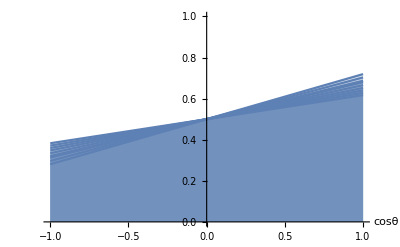

{{Sin[θ^*] (0.0176372+0.0176372 Cos[θ^*]^2-0.0532346 Cos[ϕ^*] Sin[θ^*]+0.0840918 Sin[θ^*]^2+Cos[θ^*] (-0.027471+0.0414581 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0176372+0.0176372 Cos[θ^*]^2-0.0532346 Cos[ϕ^*] Sin[θ^*]+0.0840918 Sin[θ^*]^2+Cos[θ^*] (-0.0352339+0.0531735 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0176372+0.0176372 Cos[θ^*]^2-0.0532346 Cos[ϕ^*] Sin[θ^*]+0.0840918 Sin[θ^*]^2+Cos[θ^*] (-0.0429967+0.0648888 Cos[ϕ^*] Sin[θ^*]))},{Sin[θ^*] (0.0185773+0.0185773 Cos[θ^*]^2-0.0540207 Cos[ϕ^*] Sin[θ^*]+0.0822116 Sin[θ^*]^2+Cos[θ^*] (-0.0287614+0.0418175 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0185773+0.0185773 Cos[θ^*]^2-0.0540207 Cos[ϕ^*] Sin[θ^*]+0.0822116 Sin[θ^*]^2+Cos[θ^*] (-0.0371095+0.0539552 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0185773+0.0185773 Cos[θ^*]^2-0.0540207 Cos[ϕ^*] Sin[θ^*]+0.0822116 Sin[θ^*]^2+Cos[θ^*] (-0.0454576+0.0660928 Cos[ϕ^*] Sin[θ^*]))},{Sin[θ^*] (0.019509+0.019509 Cos[θ^*]^2-0.0547278 Cos[ϕ^*] Sin[θ^*]+0.0803482 Sin[θ^*]^2+Cos[θ^*] (-0.0300062+0.0420875 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.019509+0.019509 Cos[θ^*]^2-0.0547278 Cos[ϕ^*] Sin[θ^*]+0.0803482 Sin[θ^*]^2+Cos[θ^*] (-0.0389679+0.0546575 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.019509+0.019509 Cos[θ^*]^2-0.0547278 Cos[ϕ^*] Sin[θ^*]+0.0803482 Sin[θ^*]^2+Cos[θ^*] (-0.0479296+0.0672274 Cos[ϕ^*] Sin[θ^*]))}}

-Graphics3D-

{{Sin[θ^*] (0.110818-0.172606 Cos[θ^*]+0.110818 Cos[θ^*]^2+0.528364 Sin[θ^*]^2),Sin[θ^*] (0.110818-0.221381 Cos[θ^*]+0.110818 Cos[θ^*]^2+0.528364 Sin[θ^*]^2),Sin[θ^*] (0.110818-0.270156 Cos[θ^*]+0.110818 Cos[θ^*]^2+0.528364 Sin[θ^*]^2)},{Sin[θ^*] (0.116725-0.180713 Cos[θ^*]+0.116725 Cos[θ^*]^2+0.516551 Sin[θ^*]^2),Sin[θ^*] (0.116725-0.233166 Cos[θ^*]+0.116725 Cos[θ^*]^2+0.516551 Sin[θ^*]^2),Sin[θ^*] (0.116725-0.285618 Cos[θ^*]+0.116725 Cos[θ^*]^2+0.516551 Sin[θ^*]^2)},{Sin[θ^*] (0.122579-0.188534 Cos[θ^*]+0.122579 Cos[θ^*]^2+0.504842 Sin[θ^*]^2),Sin[θ^*] (0.122579-0.244842 Cos[θ^*]+0.122579 Cos[θ^*]^2+0.504842 Sin[θ^*]^2),Sin[θ^*] (0.122579-0.301151 Cos[θ^*]+0.122579 Cos[θ^*]^2+0.504842 Sin[θ^*]^2)}}

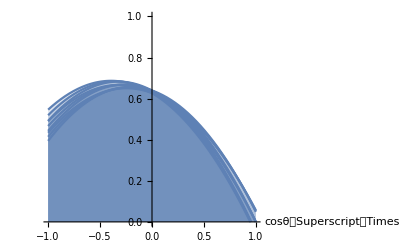

{{0.159155-0.0836208 Cos[ϕ^*],0.159155-0.0836208 Cos[ϕ^*],0.159155-0.0836208 Cos[ϕ^*]},{0.159155-0.0848556 Cos[ϕ^*],0.159155-0.0848556 Cos[ϕ^*],0.159155-0.0848556 Cos[ϕ^*]},{0.159155-0.0859663 Cos[ϕ^*],0.159155-0.0859663 Cos[ϕ^*],0.159155-0.0859663 Cos[ϕ^*]}}

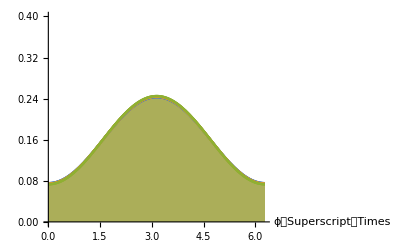

{{Sin[θ] (0.0795775+0.0215436 Cos[θ]+0.00278799 Cos[ϕ] Sin[θ]),Sin[θ] (0.0795775+0.0276314 Cos[θ]+0.00357583 Cos[ϕ] Sin[θ]),Sin[θ] (0.0795775+0.0337193 Cos[θ]+0.00436367 Cos[ϕ] Sin[θ])},{Sin[θ] (0.0795775+0.0197646 Cos[θ]+0.00255777 Cos[ϕ] Sin[θ]),Sin[θ] (0.0795775+0.0255013 Cos[θ]+0.00330017 Cos[ϕ] Sin[θ]),Sin[θ] (0.0795775+0.031238 Cos[θ]+0.00404257 Cos[ϕ] Sin[θ])},{Sin[θ] (0.0795775+0.0180111 Cos[θ]+0.00233084 Cos[ϕ] Sin[θ]),Sin[θ] (0.0795775+0.0233903 Cos[θ]+0.00302698 Cos[ϕ] Sin[θ]),Sin[θ] (0.0795775+0.0287695 Cos[θ]+0.00372311 Cos[ϕ] Sin[θ])}}

-Graphics3D-

{{Sin[θ] Sin[θ^*] (0.0554089-0.0863028 Cos[θ^*]+0.0554089 Cos[θ^*]^2+0.264182 Sin[θ^*]^2+Cos[θ] (-0.0366787+0.0941951 Cos[θ^*]-0.0366787 Cos[θ^*]^2+0.174879 Sin[θ^*]^2)),Sin[θ] Sin[θ^*] (0.0554089-0.110691 Cos[θ^*]+0.0554089 Cos[θ^*]^2+0.264182 Sin[θ^*]^2+Cos[θ] (-0.0470435+0.0941951 Cos[θ^*]-0.0470435 Cos[θ^*]^2+0.224297 Sin[θ^*]^2)),Sin[θ] Sin[θ^*] (0.0554089-0.135078 Cos[θ^*]+0.0554089 Cos[θ^*]^2+0.264182 Sin[θ^*]^2+Cos[θ] (-0.0574082+0.0941951 Cos[θ^*]-0.0574082 Cos[θ^*]^2+0.273715 Sin[θ^*]^2))},{Sin[θ] Sin[θ^*] (0.0583623-0.0903567 Cos[θ^*]+0.0583623 Cos[θ^*]^2+0.258275 Sin[θ^*]^2+Cos[θ] (-0.0384016+0.0992159 Cos[θ^*]-0.0384016 Cos[θ^*]^2+0.169942 Sin[θ^*]^2)),Sin[θ] Sin[θ^*] (0.0583623-0.116583 Cos[θ^*]+0.0583623 Cos[θ^*]^2+0.258275 Sin[θ^*]^2+Cos[θ] (-0.0495478+0.0992159 Cos[θ^*]-0.0495478 Cos[θ^*]^2+0.219268 Sin[θ^*]^2)),Sin[θ] Sin[θ^*] (0.0583623-0.142809 Cos[θ^*]+0.0583623 Cos[θ^*]^2+0.258275 Sin[θ^*]^2+Cos[θ] (-0.0606939+0.0992159 Cos[θ^*]-0.0606939 Cos[θ^*]^2+0.268594 Sin[θ^*]^2))},{Sin[θ] Sin[θ^*] (0.0612894-0.0942672 Cos[θ^*]+0.0612894 Cos[θ^*]^2+0.252421 Sin[θ^*]^2+Cos[θ] (-0.0400636+0.104192 Cos[θ^*]-0.0400636 Cos[θ^*]^2+0.165002 Sin[θ^*]^2)),Sin[θ] Sin[θ^*] (0.0612894-0.122421 Cos[θ^*]+0.0612894 Cos[θ^*]^2+0.252421 Sin[θ^*]^2+Cos[θ] (-0.052029+0.104192 Cos[θ^*]-0.052029 Cos[θ^*]^2+0.214282 Sin[θ^*]^2)),Sin[θ] Sin[θ^*] (0.0612894-0.150575 Cos[θ^*]+0.0612894 Cos[θ^*]^2+0.252421 Sin[θ^*]^2+Cos[θ] (-0.0639945+0.104192 Cos[θ^*]-0.0639945 Cos[θ^*]^2+0.263562 Sin[θ^*]^2))}}

-Graphics3D-

{{(0.5+0.135362 Cos[θ]) Sin[θ],(0.5+0.173613 Cos[θ]) Sin[θ],(0.5+0.211864 Cos[θ]) Sin[θ]},{(0.5+0.124185 Cos[θ]) Sin[θ],(0.5+0.16023 Cos[θ]) Sin[θ],(0.5+0.196274 Cos[θ]) Sin[θ]},{(0.5+0.113167 Cos[θ]) Sin[θ],(0.5+0.146965 Cos[θ]) Sin[θ],(0.5+0.180764 Cos[θ]) Sin[θ]}}

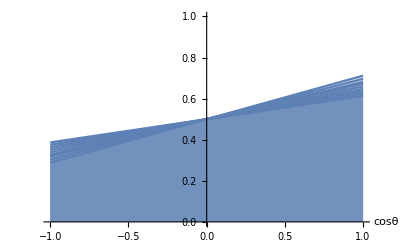

{{Sin[θ^*] (0.0176372+0.0176372 Cos[θ^*]^2-0.0514198 Cos[ϕ^*] Sin[θ^*]+0.0840918 Sin[θ^*]^2+Cos[θ^*] (-0.027471+0.0400448 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0176372+0.0176372 Cos[θ^*]^2-0.0514198 Cos[ϕ^*] Sin[θ^*]+0.0840918 Sin[θ^*]^2+Cos[θ^*] (-0.0352339+0.0513607 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0176372+0.0176372 Cos[θ^*]^2-0.0514198 Cos[ϕ^*] Sin[θ^*]+0.0840918 Sin[θ^*]^2+Cos[θ^*] (-0.0429967+0.0626767 Cos[ϕ^*] Sin[θ^*]))},{Sin[θ^*] (0.0185773+0.0185773 Cos[θ^*]^2-0.0521791 Cos[ϕ^*] Sin[θ^*]+0.0822116 Sin[θ^*]^2+Cos[θ^*] (-0.0287614+0.0403919 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0185773+0.0185773 Cos[θ^*]^2-0.0521791 Cos[ϕ^*] Sin[θ^*]+0.0822116 Sin[θ^*]^2+Cos[θ^*] (-0.0371095+0.0521158 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.0185773+0.0185773 Cos[θ^*]^2-0.0521791 Cos[ϕ^*] Sin[θ^*]+0.0822116 Sin[θ^*]^2+Cos[θ^*] (-0.0454576+0.0638397 Cos[ϕ^*] Sin[θ^*]))},{Sin[θ^*] (0.019509+0.019509 Cos[θ^*]^2-0.0528621 Cos[ϕ^*] Sin[θ^*]+0.0803482 Sin[θ^*]^2+Cos[θ^*] (-0.0300062+0.0406527 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.019509+0.019509 Cos[θ^*]^2-0.0528621 Cos[ϕ^*] Sin[θ^*]+0.0803482 Sin[θ^*]^2+Cos[θ^*] (-0.0389679+0.0527942 Cos[ϕ^*] Sin[θ^*])),Sin[θ^*] (0.019509+0.019509 Cos[θ^*]^2-0.0528621 Cos[ϕ^*] Sin[θ^*]+0.0803482 Sin[θ^*]^2+Cos[θ^*] (-0.0479296+0.0649356 Cos[ϕ^*] Sin[θ^*]))}}

-Graphics3D-

{{Sin[θ^*] (0.110818-0.172606 Cos[θ^*]+0.110818 Cos[θ^*]^2+0.528364 Sin[θ^*]^2),Sin[θ^*] (0.110818-0.221381 Cos[θ^*]+0.110818 Cos[θ^*]^2+0.528364 Sin[θ^*]^2),Sin[θ^*] (0.110818-0.270156 Cos[θ^*]+0.110818 Cos[θ^*]^2+0.528364 Sin[θ^*]^2)},{Sin[θ^*] (0.116725-0.180713 Cos[θ^*]+0.116725 Cos[θ^*]^2+0.516551 Sin[θ^*]^2),Sin[θ^*] (0.116725-0.233166 Cos[θ^*]+0.116725 Cos[θ^*]^2+0.516551 Sin[θ^*]^2),Sin[θ^*] (0.116725-0.285618 Cos[θ^*]+0.116725 Cos[θ^*]^2+0.516551 Sin[θ^*]^2)},{Sin[θ^*] (0.122579-0.188534 Cos[θ^*]+0.122579 Cos[θ^*]^2+0.504842 Sin[θ^*]^2),Sin[θ^*] (0.122579-0.244842 Cos[θ^*]+0.122579 Cos[θ^*]^2+0.504842 Sin[θ^*]^2),Sin[θ^*] (0.122579-0.301151 Cos[θ^*]+0.122579 Cos[θ^*]^2+0.504842 Sin[θ^*]^2)}}

-Graphics-

{{0.159155-0.08077 Cos[ϕ^*],0.159155-0.08077 Cos[ϕ^*],0.159155-0.08077 Cos[ϕ^*]},{0.159155-0.0819628 Cos[ϕ^*],0.159155-0.0819628 Cos[ϕ^*],0.159155-0.0819628 Cos[ϕ^*]},{0.159155-0.0830356 Cos[ϕ^*],0.159155-0.0830356 Cos[ϕ^*],0.159155-0.0830356 Cos[ϕ^*]}}

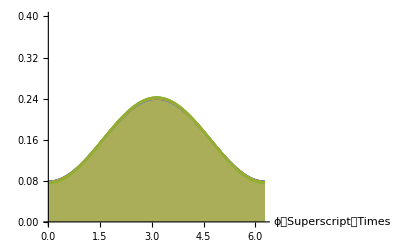

```mathematica
(* PLOTTING TOP AND ANTITOP DISTRIBUTIONS *)
Clear[Subscript[m, W],Subscript[m, t],q];
 Subscript[m, W]=Range[82.-3,82.+3,3]; Subscript[m, t]=172.5; Subscript[m, b]=4.2; q=Range[(√((Subscript[m, t]^2+Subscript[m, W]^2-Subscript[m, b]^2)^2-4 Subscript[m, t]^2 Subscript[m, W]^2))/(2 Subscript[m, t])-15,(√((Subscript[m, t]^2+Subscript[m, W]^2-Subscript[m, b]^2)^2-4 Subscript[m, t]^2 Subscript[m, W]^2))/(2 Subscript[m, t])+15,15]

Integrate[ProbTop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π},{θ,0,π},{ϕ,0,2π}]   (* should be 1!!!!! *)

(* TOP *)
Integrate[ProbTop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π}]
Plot3D[%,{θ,0,π},{ϕ,0,2π}, AxesLabel->Automatic]
Integrate[ProbTop,{ϕ,0,2π},{SuperStar[ϕ],0,2π}]
Plot3D[%/J SuperStar[J]/.{θ->ArcCos[cosθ],SuperStar[θ]->ArcCos[SuperStar[cosθ]]},{cosθ,-1,1},{SuperStar[cosθ],-1,1},AxesLabel->Automatic] (* -Sin[θ]dθ=dx => dθ=-dx/Sin[θ] and θ=ArcCos[x] *)
Integrate[ProbTop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π},{ϕ,0,2π}]
Plot[%/J/.{θ->ArcCos[cosθ]},{cosθ,-1,1},PlotRange->{0.,1.},Filling->Axis,AxesLabel->Automatic]

Integrate[ProbTop,{θ,0,π},{ϕ,0,2π}]
Plot3D[%,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π},PlotRange->{0.,0.2},AxesLabel->Automatic]
Integrate[ProbTop,{θ,0,π},{ϕ,0,2π},{SuperStar[ϕ],0,2π}]
Plot[%/SuperStar[J]/.{SuperStar[θ]->ArcCos[SuperStar[cosθ]]},{SuperStar[cosθ],-1,1},PlotRange->{0.,1.},Filling->Axis,AxesLabel->Automatic]
Integrate[ProbTop,{θ,0,π},{ϕ,0,2π},{SuperStar[θ],0,π}]
Plot[%,{SuperStar[ϕ],0,2π},PlotRange->{0.,0.4},Filling->Axis,AxesLabel->Automatic]

(* ANTITOP *)
Integrate[ProbAntitop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π}]
Plot3D[%,{θ,0,π},{ϕ,0,2π}, AxesLabel->Automatic]
Integrate[ProbAntitop,{ϕ,0,2π},{SuperStar[ϕ],0,2π}]
Plot3D[%/J SuperStar[J]/.{θ->ArcCos[cosθ],SuperStar[θ]->ArcCos[SuperStar[cosθ]]},{cosθ,-1,1},{SuperStar[cosθ],-1,1},AxesLabel->Automatic] 
Integrate[ProbAntitop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π},{ϕ,0,2π}]
Plot[%/J/.{θ->ArcCos[cosθ]},{cosθ,-1,1},PlotRange->{0.,1.},Filling->Axis,AxesLabel->Automatic]

Integrate[ProbAntitop,{θ,0,π},{ϕ,0,2π}]
Plot3D[%,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π},PlotRange->{0.,0.2},AxesLabel->Automatic]
Integrate[ProbAntitop,{θ,0,π},{ϕ,0,2π},{SuperStar[ϕ],0,2π}]
Plot[%/SuperStar[J]/.{SuperStar[θ]->ArcCos[SuperStar[cosθ]]},{SuperStar[cosθ],-1,1},PlotRange->{0.,1.},Filling->Axis,AxesLabel->Automatic]
Integrate[ProbAntitop,{θ,0,π},{ϕ,0,2π},{SuperStar[θ],0,π}]
Plot[%,{SuperStar[ϕ],0,2π},PlotRange->{0.,0.4},Filling->Axis,AxesLabel->Automatic]
```

```mathematica
'''''
```

```mathematica
Clear[Subscript[m, W],Subscript[m, t],q];
ProbTop===ProbAntitop
Simplify[ProbTop-ProbAntitop]
```

False

1/(m_t^4+1. m_t^2 m_W^2-2. m_W^4)Sin[θ] Sin[θ^*] (Cos[ϕ] Sin[θ] (0.00265968 m_t m_W^2 q+(-0.00265968 m_t^2 m_W^2+0.00265968 m_W^4) Cos[θ^*]+0.00265968 m_t m_W^2 q Cos[θ^*]^2-0.00265968 m_t^3 q Sin[θ^*]^2)+Cos[θ] (-0.033436 m_t m_W^2 q-0.033436 m_t m_W^2 q Cos[θ^*]^2+m_t m_W (-0.00265968 m_t^2+0.00265968 m_W^2) Cos[ϕ] Cos[ϕ^*] Sin[θ^*]+0.033436 m_t^3 q Sin[θ^*]^2+m_W Cos[θ^*] (0.033436 m_t^2 m_W-0.033436 m_W^3+0.00531936 m_t^2 q Cos[ϕ] Cos[ϕ^*] Sin[θ^*]))+m_t m_W Sin[θ^*] ((-0.033436 m_t^2+0.033436 m_W^2+0.066872 m_t q Cos[θ^*]) Cos[ϕ^*] Sin[θ]+(0.00265968 m_t^2-0.00265968 m_W^2-0.00531936 m_t q Cos[θ^*]) Sin[ϕ] Sin[ϕ^*]))

```mathematica
(* SOME TESTS.......SPLITTING THE PROBABILITY FOR SIMPLIFICATIONS *)
Clear[Subscript[m, W],Subscript[m, t],q];
ProbSplit=Level[TopPDF[θ,ϕ,SuperStar[θ],SuperStar[ϕ],1,Subscript[P, top]],1]
NewProb=Simplify[Sum[FullSimplify[Part[ProbSplit,i]],{i,Length[ProbSplit]}]]
```

{3/64,1/π^2,1/((m_t^2-m_W^2-2 m_t q)/m_t^2+(m_t^2-m_W^2-2 m_t q)/(2 m_W^2)+(m_t^2-m_W^2+2 m_t q)/m_t^2+(m_t^2-m_W^2+2 m_t q)/(2 m_W^2)),Sin[θ],Sin[θ^*],0.+2 √2 (((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*]) Cos[ϕ^*])/(√2 m_t m_W)+((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*]) Cos[ϕ^*])/(√2 m_t m_W)) (0.-0.9 Sin[θ]) Sin[θ^*]+(1.-0.9 Cos[θ]) (((m_t^2-m_W^2+2 m_t q) (1-Cos[θ^*])^2)/m_t^2+((m_t^2-m_W^2-2 m_t q) Sin[θ^*]^2)/m_W^2)+(1.+0.9 Cos[θ]) (((m_t^2-m_W^2-2 m_t q) (1+Cos[θ^*])^2)/m_t^2+((m_t^2-m_W^2+2 m_t q) Sin[θ^*]^2)/m_W^2)}

2.1482-(2. m_W^2)/m_t^2+(m_t^2 m_W^2)/(m_t^4+m_t^2 m_W^2-2 m_W^4)-(8. q Cos[θ^*])/m_t+((2. m_t^2-2. m_W^2) Cos[θ^*]^2)/m_t^2+(Cos[θ] (-3.6 m_t q+Cos[θ^*] (3.6 m_t^2-3.6 m_W^2-3.6 m_t q Cos[θ^*])))/m_t^2+Sin[θ]+Sin[θ^*]+((-3.6 m_t^2+3.6 m_W^2+7.2 m_t q Cos[θ^*]) Cos[ϕ^*] Sin[θ] Sin[θ^*])/(m_t m_W)+((2. m_t^2-2. m_W^2+3.6 m_t q Cos[θ]) Sin[θ^*]^2)/m_W^2

```mathematica
(* SOME TESTS.......CHECK IF/WHEN THE PDF TURNS NEGATIVE!!!!!!! *)


Reduce[{ProbTop<0},{θ,ϕ}]
```

$Aborted

```mathematica
(* TOP: GET THE MAXIMUM FOR FAST GENERATION IN THE 5D BOX θ x ϕ x θ^* x ϕ^* x MAX *)
Clear[PP,Subscript[m, W],Subscript[m, t],P,q,λ];
λ=1; Subscript[m, W]=82.; Subscript[m, t]=173.;
P={Subscript[P, x],Subscript[P, y],Subscript[P, z]};

PP[θ_,ϕ_,SuperStar[θ]:_,SuperStar[ϕ]:_,q_,λ_,P:_] :=3/(64 π^2 NORM)(( Subscript[a, 0](1+λ Cos[SuperStar[θ]])^2 + 2 Subscript[a, 1] Sin[SuperStar[θ]]^2)(1+P.uL)+
                                                           (2 Subscript[a, 2] Sin[SuperStar[θ]]^2 + Subscript[a, 3](1-λ Cos[SuperStar[θ]])^2)(1-P.uL) +
                                                             2 √2 λ(Subscript[a, 4][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 5][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uT+
                                                             2 √2 λ(Subscript[a, 6][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 7][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uN)J SuperStar[J]

Simplify[PP[θ,ϕ,SuperStar[θ],SuperStar[ϕ],q,λ,P]]
Maximize[{PP[θ,ϕ,SuperStar[θ],SuperStar[ϕ],q,λ,P],0≤θ≤π,0≤ϕ≤2 π,0≤SuperStar[θ]≤π,0≤SuperStar[ϕ]≤2 π,0≤q≤1000,-1≤Subscript[P, x]≤1,-1≤Subscript[P, y]≤1,-1≤Subscript[P, z]≤1, Subscript[P, x]^2+Subscript[P, y]^2+Subscript[P, z]^2==1},{θ,ϕ,SuperStar[θ],SuperStar[ϕ],q,Subscript[P, x],Subscript[P, y],Subscript[P, z]}]
(* not sure about Subscript[P, x]^2+Subscript[P, y]^2+Subscript[P, z]^2==1 constraint, but better than nothing!!!! *)
```

0.000949556 Sin[θ] Sin[θ^*] ((0.0115607 (67.0665+1. q) (-1.+Cos[θ^*])^2-0.0514575 (-67.0665+1. q) Sin[θ^*]^2) (1-P_z Cos[θ]-P_x Cos[ϕ] Sin[θ]-P_y Sin[θ] Sin[ϕ])+(0.0000334124 (23205.-346. q) (1+Cos[θ^*])^2+0.0514575 (67.0665+1. q) Sin[θ^*]^2) (1+P_z Cos[θ]+P_x Cos[ϕ] Sin[θ]+P_y Sin[θ] Sin[ϕ])-0.097561 (-67.0665+1. q Cos[θ^*]) Cos[ϕ^*] Sin[θ^*] (-1. P_z Sin[θ]+Cos[θ] (P_x Cos[ϕ]+P_y Sin[ϕ]))-0.097561 (-67.0665+1. q Cos[θ^*]) Sin[θ^*] (P_y Cos[ϕ]-1. P_x Sin[ϕ]) Sin[ϕ^*])

{0.0892307,{θ→1.5708,ϕ→2.01824,θ^*→1.78409,ϕ^*→2.11481,q→1000.,P_x→-0.669233,P_y→0.721901,P_z→0.176031}}

```mathematica
(* ANTITOP: GET THE MAXIMUM FOR FAST GENERATION IN THE 5D BOX θ x ϕ x θ^* x ϕ^* x MAX *)
Clear[PPanti,Subscript[m, W],Subscript[m, t],P,q,λ];
λ=-1; Subscript[m, W]=82.; Subscript[m, t]=173.;
P={Subscript[P, x],Subscript[P, y],Subscript[P, z]};

PPanti[θ_,ϕ_,SuperStar[θ]:_,SuperStar[ϕ]:_,q_,λ_,P:_] :=3/(64 π^2 NORM)(( Subscript[a, 3](1+λ Cos[SuperStar[θ]])^2 + 2 Subscript[a, 2] Sin[SuperStar[θ]]^2)(1+P.uL)+
                                                           (2 Subscript[a, 1] Sin[SuperStar[θ]]^2 + Subscript[a, 0](1-λ Cos[SuperStar[θ]])^2)(1-P.uL) +
                                                             2 √2 λ(Subscript[a, 5][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 4][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uT+
                                                             2 √2 λ(Subscript[a, 7][SuperStar[ϕ]](1+λ Cos[SuperStar[θ]])+Subscript[a, 6][SuperStar[ϕ]](1-λ Cos[SuperStar[θ]]))Sin[SuperStar[θ]]P.uN)J SuperStar[J]

Simplify[PPanti[θ,ϕ,SuperStar[θ],SuperStar[ϕ],q,λ,P]]
Maximize[{PPanti[θ,ϕ,SuperStar[θ],SuperStar[ϕ],q,λ,P],0≤θ≤π,0≤ϕ≤2 π,0≤SuperStar[θ]≤π,0≤SuperStar[ϕ]≤2 π,0≤q≤1000,-1≤Subscript[P, x]≤1,-1≤Subscript[P, y]≤1,-1≤Subscript[P, z]≤1, Subscript[P, x]^2+Subscript[P, y]^2+Subscript[P, z]^2==1},{θ,ϕ,SuperStar[θ],SuperStar[ϕ],q,Subscript[P, x],Subscript[P, y],Subscript[P, z]}]
```

0.000949556 Sin[θ] Sin[θ^*] ((0.0000334124 (23205.-346. q) (1+Cos[θ^*])^2+0.0514575 (67.0665+1. q) Sin[θ^*]^2) (1-P_z Cos[θ]-P_x Cos[ϕ] Sin[θ]-P_y Sin[θ] Sin[ϕ])+(0.0115607 (67.0665+1. q) (-1.+Cos[θ^*])^2-0.0514575 (-67.0665+1. q) Sin[θ^*]^2) (1+P_z Cos[θ]+P_x Cos[ϕ] Sin[θ]+P_y Sin[θ] Sin[ϕ])+0.097561 (-67.0665+1. q Cos[θ^*]) Cos[ϕ^*] Sin[θ^*] (-1. P_z Sin[θ]+Cos[θ] (P_x Cos[ϕ]+P_y Sin[ϕ]))+0.097561 (-67.0665+1. q Cos[θ^*]) Sin[θ^*] (P_y Cos[ϕ]-1. P_x Sin[ϕ]) Sin[ϕ^*])

{0.0892307,{θ→1.5708,ϕ→0.118143,θ^*→1.78409,ϕ^*→4.65363,q→1000.,P_x→-0.97385,P_y→0.226313,P_z→-0.0199714}}

```mathematica
(* CONSTRUCT THE FULLY DIFFERENTIAL CROSS SECTION, FUNCTION OF (θ,ϕ) *)

Clear[Subscript[m, W],Subscript[m, t],q];

(* TOP *)
Integrate[ProbTop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π}]
(* ANTITOP *)
Integrate[ProbAntitop,{SuperStar[θ],0,π},{SuperStar[ϕ],0,2π}]
```

0.00116289 Sin[θ] Sin[θ^*] ((0.0000272829 (23205.-346. q) (1+Cos[θ^*])^2+0.0420176 (67.0665+1. q) Sin[θ^*]^2) (1-P_z Cos[θ]-P_x Cos[ϕ] Sin[θ]-P_y Sin[θ] Sin[ϕ])+(0.00943988 (67.0665+1. q) (-1.+Cos[θ^*])^2-0.0420176 (-67.0665+1. q) Sin[θ^*]^2) (1+P_z Cos[θ]+P_x Cos[ϕ] Sin[θ]+P_y Sin[θ] Sin[ϕ])+0.0796634 (-67.0665+1. q Cos[θ^*]) Cos[ϕ^*] Sin[θ^*] (-1. P_z Sin[θ]+Cos[θ] (P_x Cos[ϕ]+P_y Sin[ϕ]))+0.0796634 (-67.0665+1. q Cos[θ^*]) Sin[θ^*] (P_y Cos[ϕ]-1. P_x Sin[ϕ]) Sin[ϕ^*])

{1.16987,{θ→1.78114,ϕ→4.52161×10^-11,θ^*→1.90558,ϕ^*→5.36804,q→10000.,P_x→-1.,P_y→1.,P_z→1.}}

$Aborted

$Aborted